ReplaceAll::reps: {#1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

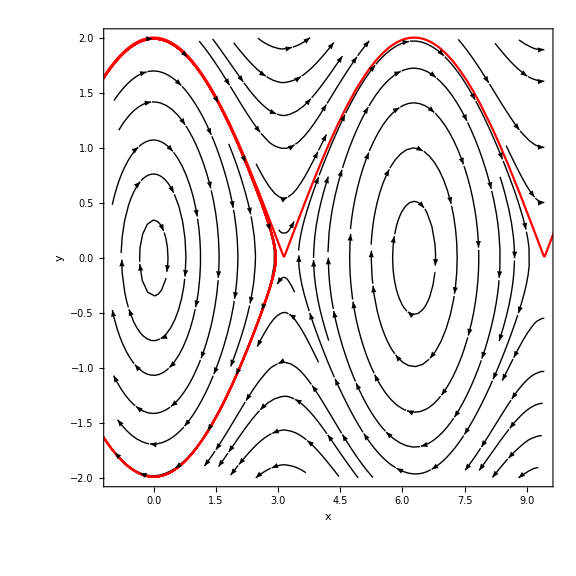

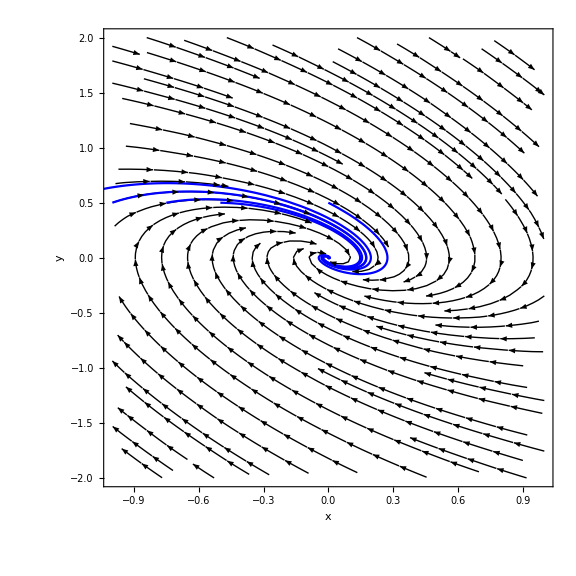

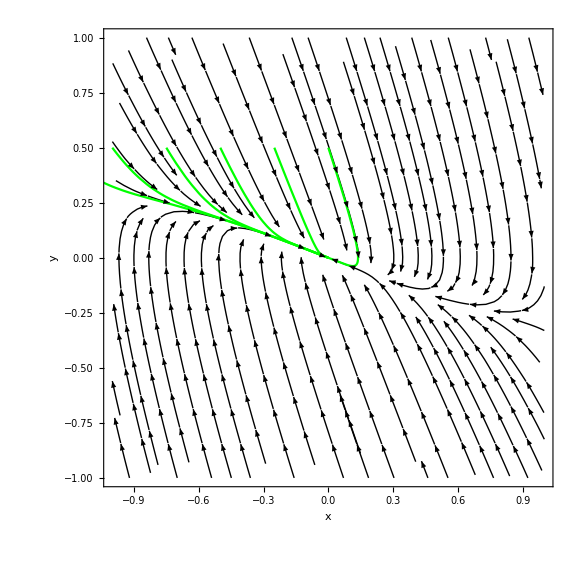

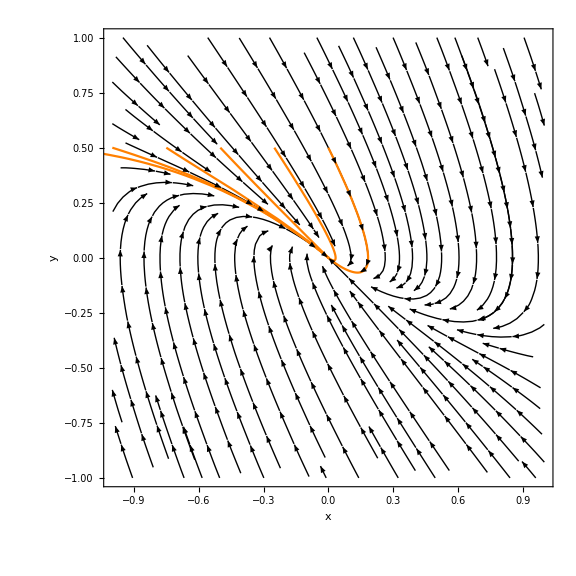

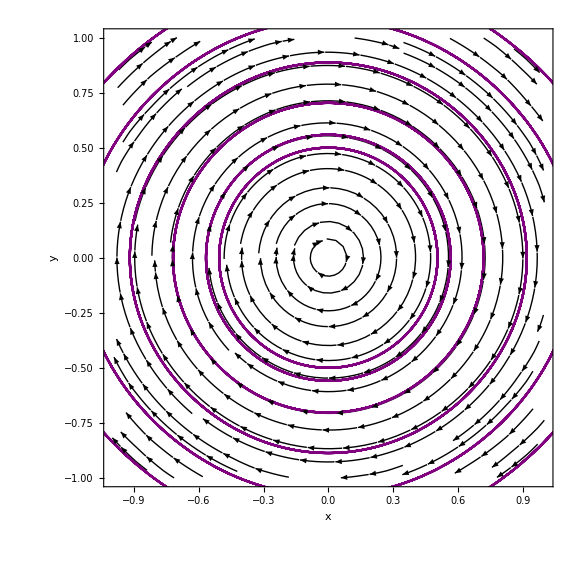

```mathematica
ClearAll["Global`*"]

(*Define the system of differential equations*)
sigma1=0;(*Saddle point*)sigma21=1;(*Stable Spiral*)sigma22=3;(*Stable Node*)sigma23=2;(*Degenerate Node*)sigma24=0;(*Center*)eq1=x'[t]==y[t];
eq2=y'[t]==-Sin[x[t]]-sigma1*y[t];
eq21=y'[t]==-Sin[x[t]]-sigma21*y[t];
eq22=y'[t]==-Sin[x[t]]-sigma22*y[t];
eq23=y'[t]==-Sin[x[t]]-sigma23*y[t];
eq24=y'[t]==-Sin[x[t]]-sigma24*y[t];

(*Offset of the fixed point*)
delta1=0.2;
delta2=0.5;

(*Define the fixed points*)
fixedPoint1={-π,0};
fixedPoint2={0,0};

(*Define the system and the initial conditions for multiple trajectories*)
system1={eq1,eq2};
system21={eq1,eq21};
system22={eq1,eq22};
system23={eq1,eq23};
system24={eq1,eq24};

numTrajectories=6;

initialConditions1=Table[{x[0]==fixedPoint1[[1]]+delta1,y[0]==fixedPoint1[[2]]+delta1-i},{i,0,(numTrajectories-1) delta1,delta1}];
initialConditions2=Table[{x[0]==fixedPoint2[[1]]-i*delta2,y[0]==fixedPoint2[[2]]+delta2},{i,0,(numTrajectories-1) delta2,delta2}];

t0=0;
tMax=40;

(*Solve the system of differential equations for multiple trajectories*)
sol1=Table[NDSolve[{system1,initCond},{x,y},{t,t0,tMax}],{initCond,initialConditions1}];
sol21=Table[NDSolve[{system21,initCond},{x,y},{t,t0,tMax}],{initCond,initialConditions2}];
sol22=Table[NDSolve[{system22,initCond},{x,y},{t,t0,tMax}],{initCond,initialConditions2}];
sol23=Table[NDSolve[{system23,initCond},{x,y},{t,t0,tMax}],{initCond,initialConditions2}];
sol24=Table[NDSolve[{system24,initCond},{x,y},{t,t0,tMax}],{initCond,initialConditions2}];

(* Plot the phase portraint*) 
ps10 = StreamPlot[{y, -Sin[x] - sigma1*y}, {x, -1, 3*Pi}, {y, -2, 2}, 
   PlotRange -> All, ImageSize -> Large, ColorFunction -> (Black), 
   StreamStyle -> Directive[Black], StreamColorFunction->None];

(* Plot the phase portraint*) 
ps21 = StreamPlot[{y, -Sin[x] - sigma21*y}, {x, -1, 1}, {y, -2, 2}, 
   PlotRange -> All, ImageSize -> Large, ColorFunction -> (Black), 
   StreamStyle -> Directive[Black], StreamColorFunction->None];
ps22 = StreamPlot[{y, -Sin[x] - sigma22*y}, {x, -1, 1}, {y, -1, 1}, 
   PlotRange -> All, ImageSize -> Large, ColorFunction -> (Black), 
   StreamStyle -> Directive[Black], StreamColorFunction->None];
ps23 = StreamPlot[{y, -Sin[x] - sigma23*y}, {x, -1, 1}, {y, -1, 1}, 
   PlotRange -> All, ImageSize -> Large, ColorFunction -> (Black), 
   StreamStyle -> Directive[Black], StreamColorFunction->None];
ps24 = StreamPlot[{y, -Sin[x] - sigma24*y}, {x, -1, 1}, {y, -1, 1}, 
   PlotRange -> All, ImageSize -> Large, ColorFunction -> (Black), 
   StreamStyle -> Directive[Black], StreamColorFunction->None];

(*Plot trajectories for the different systems*)
p10=ParametricPlot[Evaluate[{x[t],y[t]}/. #]&/@sol1,{t,t0,tMax},PlotStyle->Red];
p21=ParametricPlot[Evaluate[{x[t],y[t]}/. #]&/@sol21,{t,t0,tMax},PlotStyle->Blue];
p22=ParametricPlot[Evaluate[{x[t],y[t]}/. #]&/@sol22,{t,t0,tMax},PlotStyle->Green];
p23=ParametricPlot[Evaluate[{x[t],y[t]}/. #]&/@sol23,{t,t0,tMax},PlotStyle->Orange];
p24=ParametricPlot[Evaluate[{x[t],y[t]}/. #]&/@sol24,{t,t0,tMax},PlotStyle->Purple];

(*Label the plot*)
Show[ ps10, p10,
  FrameLabel -> {"x", "y"}
]
Show[ ps21, p21,
  FrameLabel -> {"x", "y"}
]
Show[ ps22, p22,
  FrameLabel -> {"x", "y"}
]
Show[ ps23, p23,
  FrameLabel -> {"x", "y"}
]
Show[ ps24, p24,
  FrameLabel -> {"x", "y"}
]
```